```mathematica
http://blog.wolfram.com/2012/01/04/how-to-count-cells-annihilate-sailboats-and-warp-the-mona-lisa/
```

Try Vision processing in Mathematica
Aaron Becker, Jan 1, 2015

```mathematica
rbc = -Graphics-
```

-Graphics-

```mathematica
(*b=FillingTransform[Binarize[rbc]]*)
b=Binarize[Blur[rbc,3]]
```

-Graphics-

```mathematica
GradFilter 1 is bad -- doesn't get background in one piece.  3 was standard.  5 splits umbrellas.  2 is ok., 2 works for when I don't do the background.  3 good too.
```

```mathematica
distT=DistanceTransform[b,Padding-> 0];
marker = MaxDetect[ImageAdjust[distT],0.02];
w = WatershedComponents[GradientFilter[b,3],marker, Method-> "Rainfall"];
Colorize[w]
```

-Graphics-

```mathematica
cells = SelectComponents[w,"Count",1000<#<5000 &];
measures = ComponentMeasurements[cells, {"Centroid","EquivalentDiskRadius","Label"}];
Show[rbc,Graphics[{White, Circle@@ # &/@(measures⟦All,2,1
;;2⟧),MapThread[Text,{measures⟦All,2,3⟧,measures⟦All,2,1⟧}]}],ImageSize->Large]
```

-Graphics-

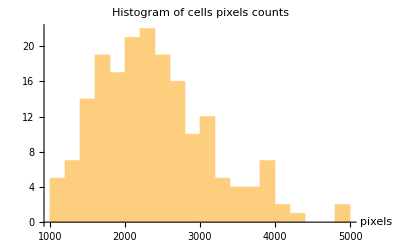

```mathematica
Histogram[ComponentMeasurements[cells,"Count"]⟦All,2⟧,20,AxesLabel-> {"pixels"},PlotLabel-> "Histogram of cells pixels counts"]
```

```mathematica
cells = SelectComponents[w,"Count",500<#<5000 &];
measures = ComponentMeasurements[cells, {"Centroid","EquivalentDiskRadius","Label"}];
Show[rbc,Graphics[{White, Circle@@ # &/@(measures⟦All,2,1
;;2⟧),MapThread[Text,{measures⟦All,2,3⟧,measures⟦All,2,1⟧}]}],ImageSize->Large]
```

-Graphics-

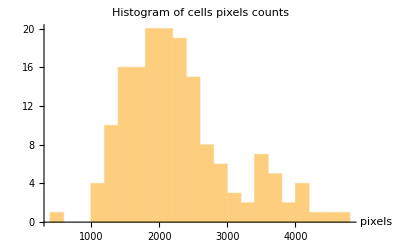

```mathematica
Histogram[ComponentMeasurements[cells,"Count"]⟦All,2⟧,20,AxesLabel-> {"pixels"},PlotLabel-> "Histogram of cells pixels counts"]
```

### Ideas : can I find an image channel where the LEDS provide a great seed value for WatershedComponents?

```mathematica
ColorSeparate[rbc]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ColorConvert[rbc,"Grayscale"]
```

-Graphics-

```mathematica
ColorSeparate[ColorConvert[rbc,"CMYK"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
KfromCMYK=-Graphics-
```

-Graphics-

```mathematica
Binarize[KfromCMYK,.9]
```

-Graphics-

```mathematica
MaxDetect[rbc]
```

-Graphics-

```mathematica
rbc
```

-Graphics-

```mathematica
rbcSHARP=Sharpen[rbc,25]
```

-Graphics-

```mathematica
ImageDeconvolve[rbc,GaussianMatrix[3]]
```

-Graphics-

```mathematica
ImageConvolve[rbc, {{-1,0,1},{-2,0,2},{-1,0,1}}]
```

-Graphics-

```mathematica
soebel = Image[Sqrt[ImageData[ImageConvolve[rbc, {{1,0},{0,-1}}]]^2+ImageData[ImageConvolve[rbc, {{0,1},{-1,0}}]]^2]]
```

-Graphics-

```mathematica
ColorNegate[soebel]
```

-Graphics-

```mathematica
img=-Graphics-;
template=-Graphics-;mask=-Graphics-;
pos=Position[Flatten[ImageData[mask]],1];
f:=NormalizedSquaredEuclideanDistance[Extract[#1,pos],Extract[#2,pos]]&;
{xmaskedmap=ImageCorrelate[img,template,f],
HighlightImage[img,Dilation[ColorNegate[Binarize[xmaskedmap,0.25]], DiskMatrix[15]]]}
```

{-Graphics-,-Graphics-}

```mathematica
pos=Position[Flatten[ImageData[mask]],1];
f:=NormalizedSquaredEuclideanDistance[Extract[#1,pos],Extract[#2,pos]]&;
{xmaskedmap=ImageCorrelate[img,template,f],
HighlightImage[img,Dilation[ColorNegate[Binarize[xmaskedmap,0.25]], DiskMatrix[15]]]}
```